# Sustain Compressor

## First order lowpass filter

```mathematica
firstOrderLowpass[X_,fc_,sampleRate_]:=Module[{γ, a0, a1, b0, b1,out,i,za,zb},
out = X;

Assert[fc <sampleRate/2];

γ = N[Tan[ π fc / sampleRate]];
a0 = γ + 1;
b0 = γ / a0;
b1 = b0;
a1 = (γ-1)/a0;

za = 0;
zb = 0;

For[i=1,i≤Length[X],i++,
out[[i]] = b0 X[[i]] + b1 zb - a1 za;
za = out[[i]];
zb = X[[i]];
];

out
]
```

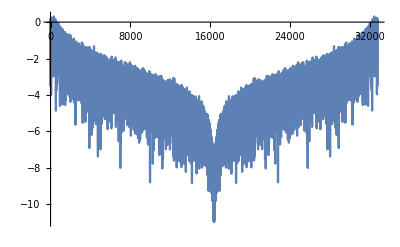

```mathematica
(* test *)
ListLinePlot[
Log[Abs[Fourier[
firstOrderLowpass[RandomReal[{-1,1},4096*8],1000,48000]
]]]
]
```

## Compressor tests

The basic idea is to have several stages of compression with different thresholds. Compressors with lower thresholds have longer attack and release times. This results in a kind of saturating limiter but with much lower harmonic distortion. 

For now we simply use lowpass filters to compute the volume envelope, so that the attack and release times are equal.

## Limiter unit

A single stage limiter unit consists of an envelope follower and a gain reduction that attenuates the output if it exceeds a given threshold.

```mathematica
dBToGain[dB_]:=10^(dB/20)
gainToDb[g_]:=20 Log10[g]
ramp[x_]:=(x +Abs[x])/2

limiterUnit[X_,thresholdDb_,fc_,sampleRate_]:=Module[{envelope, envelopeDb, excessDb,gainReductionDb, controlSignal},
envelope = 
firstOrderLowpass[
firstOrderLowpass[
firstOrderLowpass[Abs[X],fc, sampleRate],
fc,sampleRate],
fc, sampleRate];

envelopeDb = gainToDb[envelope];
excessDb = ramp[envelopeDb - thresholdDb];
gainReductionDb = -excessDb;
controlSignal = dBToGain[gainReductionDb];

X * controlSignal
]

asymptoticLimit[X_]:=X / (1+ Abs[X])

limiterUnit2[X_,fc_,sampleRate_]:=Module[{envelope,limitedEnvelope,controlSignal},
envelope = 
firstOrderLowpass[
firstOrderLowpass[
firstOrderLowpass[Abs[X],fc, sampleRate],
fc,sampleRate],
fc, sampleRate];

limitedEnvelope = asymptoticLimit[envelope];
controlSignal = (limitedEnvelope+ 0.0001) / (envelope+ 0.0001);

X * controlSignal
]
```

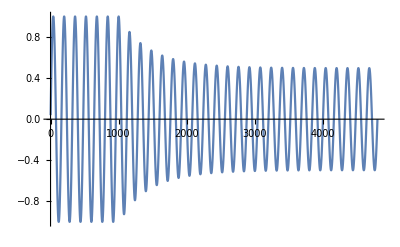

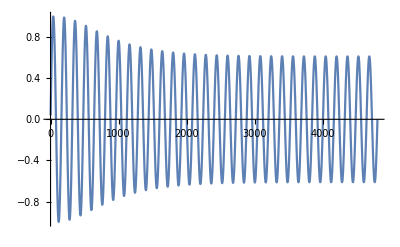

```mathematica
(* test limiter unit *)
freq = 300;
sampleRate =48000;
fc = 20;
thresholdDb = -10;
testInput = Table[Sin[freq 2π t / sampleRate],{t,1,0.1 sampleRate}];
testOutput = limiterUnit[testInput,thresholdDb,fc,sampleRate];
ListLinePlot[testOutput,PlotRange->All]
testOutput = limiterUnit2[testInput,fc,sampleRate];
ListLinePlot[testOutput,PlotRange->All]
```

## Multi-stage limiter

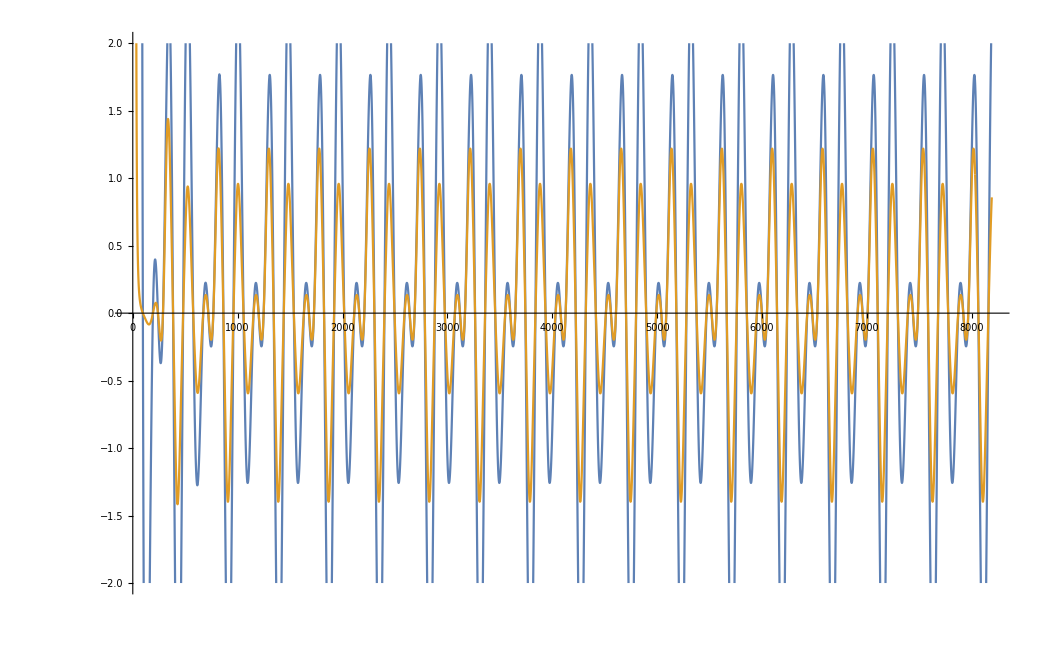

-Graphics-

-Graphics-

```mathematica
freq = 200;
sampleRate =48000;
fc = 100;
thresholdDb = -6;
inputGainDb = 60;
length = 2^13;
testInput =dBToGain[inputGainDb] Table[2^(N[-2t]/sampleRate)(Sin[freq 2π N[t] / sampleRate]+Sin[(3/2)freq 2π N[t] / sampleRate]),{t,1,length}];

mp = 4;

testOutput1 =
limiterUnit2[testInput,fc,sampleRate];


testOutput2 =
limiterUnit2[
limiterUnit2[testInput,fc,sampleRate],
mp fc,sampleRate];

ListLinePlot[{testOutput1,testOutput2},PlotRange->{-2,2}]
ListPlay[testInput, SampleRate->sampleRate]
ListPlay[testOutput2, SampleRate->sampleRate]
```